1 - 10 Parametric representations
What curves are represented by the following? Sketch them.

1.  {3 + 2 Cos[t], 2 Sin[t], 0}

```mathematica
ParametricPlot3D[{3+2 Cos[t],2 Sin[t],0},{t,0,2 π},ImageSize->300]
```

-Graphics3D-

Above: this is a circle. Center {3, 0}, radius 2.

3.  {0,t,t^3}

```mathematica
ParametricPlot3D[{0,t,t^3},{t,0,2 π},AspectRatio->1,ImageSize->300]
```

-Graphics3D-

Above: this looks like half of a ‘u’ shape. The text answer calls it a cubic parabola.

5.  {2 + 4 Cos[t], 1 + Sin[t], 0}

```mathematica
ParametricPlot3D[{2+4 Cos[t],1+Sin[t],0},{t,0,2 π},AspectRatio->1,ImageSize->300,PlotStyle->Thickness[0.004]]
```

-Graphics3D-

Above: this looks like an ellipse.

7.  {4 Cos[t], 4 Sin[t], 3 t}

```mathematica
ParametricPlot3D[{4 Cos[t],4 Sin[t],3 t},{t,0,2 π},AspectRatio->1,ImageSize->300,PlotStyle->Thickness[0.004]]
```

-Graphics3D-

Above: this is a helix.

9.  {Cos[t], Sin[2 t], 0}

```mathematica
ParametricPlot3D[{ Cos[t],1+Sin[2 t],0},{t,0,2 π},AspectRatio->1,ImageSize->300,PlotStyle->Thickness[0.004]]
```

-Graphics3D-

Above: this is a figure-8, a “Lissajous”.

11 - 20 Find a parametric representation

11.  Circle in the plane z = 1 with center {3, 2} and passing through the origin.

```mathematica
Clear["Global`*"]
```

I need the radius.

```mathematica
e1=Norm[{3,2}]
```

√13

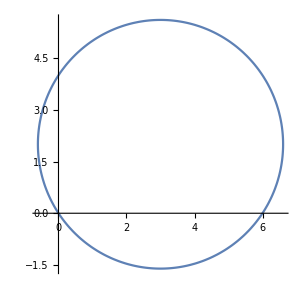

```mathematica
e2=ParametricPlot[{3+√13 Cos[t],2+√13 Sin[t]},{t,0,2 π},ImageSize->300]
```

The above result in 2D shows that the equation works.  Only necessary to add the z-plane requirement.

```mathematica
e3=ParametricPlot3D[{3+√13 Cos[t],2+√13 Sin[t],1},{t,0,2 π},ImageSize->300]
```

-Graphics3D-

With the pseudo-parallax effect, it is hard to tell whether the origin is part of the circle.

```mathematica
e4=Solve[3+√13 Cos[t]==0&&2+√13 Sin[t]==0]
```

{{t→ConditionalExpression[-π+ArcTan[2/3]+2 π C[1],C[1]∈Integers]}}

```mathematica
e5=N[π+ArcTan[2/3]]
```

3.7296

Since this result points to a number in the defining interval of the function, I take it to show that (0,0,1) is in the circle.

13.  Straight line through {2, 1, 3} in the direction of i + 2j.

```mathematica
Clear["Global`*"]
```

```mathematica
Show[ParametricPlot3D[{u+2,2 u+1,3},{u,-3,3},PlotStyle->{Red,Thickness[0.03],Opacity[.2]},ImageSize->200],ParametricPlot3D[{t+2,2 t+1,3},{t,-3,3},PlotStyle->{Black,Thickness[0.003]}],ParametricPlot3D[{t+1, 2 t+2,0},{t,-3,3},PlotStyle->{Teal,Thickness[0.003]}],ListPointPlot3D[{{2,1,3},{1,2,0}},PlotStyle->Blue],Graphics3D[{Text["2,1,3",{2.2,1.2,3.2}],Text["1,2,0",{1.2,2.2,.2}]}]]
```

-Graphics3D-

The red line goes through the specified point and has the same direction as [1,2,0]. The text answer line (black) runs inside the red line.

15.  Straight line y = 4x -1, z = 5x.

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[y==4 x-1&&z==5 x&&x==1]
```

{{x→1,y→3,z→5}}

```mathematica
Solve[y==4 x-1&&z==5 x&&x==4]
```

{{x→4,y→15,z→20}}

```mathematica
e1=Show[ParametricPlot3D[{3 u+1,12 u+3,15 u+5},{u,-3,3},PlotStyle->{Red,Thickness[0.005],Opacity[.4]}],ParametricPlot3D[{t,4 t-1,5 t},{t,-3,3},PlotStyle->Thickness[0.003]],ListPointPlot3D[{{1,3,5},{4,15,20}},PlotStyle->Red]]
```

-Graphics3D-

Above: the line shown meets the requirements. The text answer line is shown within.

17. Circle 1/2 x^2+y^2 = 1, z = y.

```mathematica
Clear["Global`*"]
```

This didn’t look like a circle when I first did the problem. This problem is treated in the s.m., so I take that general direction. It looks like an ellipse, and the form of the equation can be changed.
e1=x^2/(√2)^2+y^2=1. From the general form, it can be seen that it is an ellipse with semi-major axis of √2. Putting that into parametric form would be (√2cos u+a)+(sin u+b), where the a and b are center locations. Here both are zero.

```mathematica
ParametricPlot3D[{√2 Cos[u],Sin[u],Sin[u]},{u,0,2Pi},AxesLabel->{x,y,z},PlotStyle->Thickness[0.004],ImageSize->300]
```

-Graphics3D-

The z part of the equation just mirrors y, it’s not necessary to ponder what effect it might have.  But after it is plotted, it can be seen to be a true circle, due to that z component, which represents its tilt away from the xy-plane.

19.  Hyperbola 4x^2 - 3y^2, z = -2

```mathematica
Clear["Global`*"]
```

Hyperbola. I looked this one up before. The parametric version is a/(cos t),b tan t. In this case a=1,b=-(√3)/2.

```mathematica
Show[ParametricPlot3D[{1/Cos[u],-(√3)/2 Tan[u],-2},{u,0,2 π},Exclusions->{Cos[u]==0},ImageSize->300,PlotStyle->{Thickness[0.015],Opacity[.4]}],ParametricPlot3D[{{Cosh[t],(√3)/2 Sinh[t],-2},{-Cosh[t],(√3)/2 Sinh[t],-2}},{t,-2 π,2 π},ImageSize->300,PlotStyle->{Red,Thickness[0.003]}]]
```

-Graphics3D-

Three things going on here. The first is my own plot of the hyperbola, skinny black. The second and third are the fatter versions of the hyperbola, but only the red one is contained in the text answer. It deficient to me because it is necessary to show two functions in order to get both sides of the hyperbola.

21.  Orientation. Explain why setting t = -t* reverses the orientation of {a Cos[t], a Sin[t], 0}.

23. CAS project. Famous curves in polar form. Use your CAS to graph the following curves given in polar form ρ = ρ(θ), ρ^2 = x^2 + y^2, Tan[θ] = y/x, and investigate their form depending on parameters a and b.

ρ=a θ | Spiral of Archimedes
ρ=a ⅇ^(b θ) | Logarithmic spiral
ρ=(2a Sin[θ]^2)/Cos[θ] | Cissoid of Diocles
ρ=a/Cos[θ]+b | Conchoid of Nicomedes
ρ=a/θ | Hyperbolic spiral
ρ=(3a Sin[2θ])/(Cos[θ]^3+Sin[θ]^3) | Folium of Descartes
ρ=2a Sin[3θ]/Sin[2θ] | Maclaurin's trisectrix
ρ=2a Cos[θ]+b | Pascal's snail

24 - 28 Tangent
Given a curve C: r[t], find a tangent vector r'[t], a unit tangent vector u'[t], and the tangent of C at P. Sketch curve and tangent.

25.  r[t] = {10 Cos[t], 1, 10 Sin[t]}, P : {6, 1, 8}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=Solve[10 Cos[t]==6&&10 Sin[t]==8]
```

{{t→ConditionalExpression[ArcTan[4/3]+2 π C[1],C[1]∈Integers]}}

```mathematica
e2=e1[[1,1,2,1]]
```

ArcTan[4/3]+2 π C[1]

```mathematica
e3=e2/.C[1]->0
```

ArcTan[4/3]

Above: this is the value that satisfies the problem vector function for the given point.

```mathematica
e4=r[t_]={10 Cos[t],1,10 Sin[t]}
```

{10 Cos[t],1,10 Sin[t]}

```mathematica
e5=r[ArcTan[4/3]]
```

{6,1,8}

The above shows that P corresponds to t=ArcTan[4/3] with regard to the given function r.

```mathematica
e6=r'[ArcTan[4/3]]
```

{-8,0,6}

```mathematica
e7=e5+w e6
```

{6-8 w,1,8+6 w}

Above: this is the tangent of C:r[t] at P, called Q(w).

Below: using the (8) on p. 384 of the text, I find the unit tangent at P,

```mathematica
e8=r'[t]
```

{-10 Sin[t],0,10 Cos[t]}

```mathematica
e9=Norm[e8]
```

√(100 Abs[Cos[t]]^2+100 Abs[Sin[t]]^2)

```mathematica
e10=FullSimplify[e9]
```

10 √(Abs[Cos[t]]^2+Abs[Sin[t]]^2)

```mathematica
e11=10/.√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)->1
```

10

```mathematica
e12=e8 1/e11
```

{-Sin[t],0,Cos[t]}

Above: this is the unit tangent. The above answers agree with the text.

```mathematica
e14=e12[{6,1,8}]
```

{-Sin[t],0,Cos[t]}[{6,1,8}]

```mathematica
e13=Show[ParametricPlot3D[{10 Cos[t],1,10 Sin[t]},{t,-3.275,3},PlotStyle->{Red,Thickness[0.005],Opacity[.4]},ImageSize->300],ListPointPlot3D[{{6,1,8},{0,1,0}},PlotStyle->Blue],ParametricPlot3D[{6-8 w,1,8+6 w},{w,-1,1},PlotStyle->{Green,Thickness[0.005]}],Graphics3D[{Text["{6,1,8}",{6.7,1,8.7}]}]]
```

-Graphics3D-

27.  r[t]={t,1/t,0}, P:{2, 1/2, 0}

```mathematica
Clear["Global`*"]
```

By inspection it can be seen that P represents t=2, as demonstrated in e2.

```mathematica
e1=r[t_]={t,1/t,0}
```

{t,1/t,0}

```mathematica
e2=r[2]
```

{2,1/2,0}

```mathematica
e3=r'[t]
```

{1,-1/t^2,0}

```mathematica
e4=r'[2]
```

{1,-1/4,0}

```mathematica
e5=e2+w e4
```

{2+w,1/2-w/4,0}

Above: the tangent of C:r[t], matching the answer in the text.

```mathematica
e9=Norm[e3]
```

√(1+1/Abs[t]^4)

```mathematica
e10=e3/e9
```

{1/(√(1+1/Abs[t]^4)),-1/(t^2 √(1+1/Abs[t]^4)),0}

Above: this is the unit tangent.

```mathematica
e13=Show[ParametricPlot3D[{t,1/t,0},{t,-3.5,3.5},PlotStyle->{Red,Thickness[0.005],Opacity[.4]},ImageSize->300],ListPointPlot3D[{{2,1/2,0},{0,0,0}},PlotStyle->Blue],ParametricPlot3D[{2+w,1/2-w/4,0},{w,-1,1},PlotStyle->{Green,Thickness[0.005]}],Graphics3D[{Text["{2,1/2,0}",{2.1,1,0}]}]]
```

-Graphics3D-

29 - 32 Length
Find the length and sketch the curve.

29.  Catenary r[t] = {t, Cosh[t]} from t = 0 to t = 1.

```mathematica
Clear["Global`*"]
```

```mathematica
e1=r[t_]={t,Cosh[t]}
```

{t,Cosh[t]}

```mathematica
e2=r'[t]
```

{1,Sinh[t]}

```mathematica
e3=len=Integrate[√(r'[t].r'[t]) ,{t,0,1}]
```

Sinh[1]

```mathematica
e4=N[Sinh[1]]
```

1.1752

Above in green: two values which agree with the answer in the text.

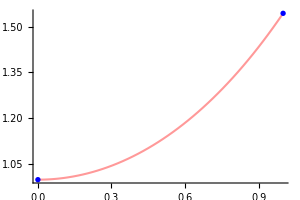

```mathematica
Show[ParametricPlot[{t,Cosh[t]},{t,0,1},PlotStyle->{Red,Thickness[0.005],Opacity[.4]},ImageSize->300],ListPlot[{{0,Cosh[0]},{1,Cosh[1]}},PlotStyle->Blue],AxesOrigin->Automatic]
```

31.  Circle r[t] = {a Cos[t], a Sin[t]} from {a, 0} to {0, a}.

```mathematica
Clear["Global`*"]
```

```mathematica
e1=r[t_]={a Cos[t],a Sin[t]}
```

{a Cos[t],a Sin[t]}

```mathematica
e2=r'[t]
```

{-a Sin[t],a Cos[t]}

```mathematica
e3=len=Integrate[√(r'[t].r'[t]),{t,0,π/2}]
```

(√(a^2) π)/2

Above: The answer shown agrees with the text. Integration limits based on initial values.

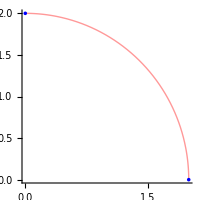

```mathematica
Show[ParametricPlot[{2 Cos[t],2 Sin[t]},{t,0,π/2},PlotStyle->{Red,Thickness[0.005],Opacity[.4]},ImageSize->200],ListPlot[{{2 Cos[0],2 Sin[0]},{2 Cos[π/2],2 Sin[π/2]}},PlotStyle->Blue],AxesOrigin->Automatic]
```

33. Plane curve. Show that numbered line (10) on p. 385 implies ℓ=∫_a^b 1+(y')^2 ⅆx for the length of a plane curve C: y = f[x], z = 0, and a = x = b.

35 - 46 Curves in mechanics
Forces acting on moving objects (cars, airplanes, ships, etc.) require the engineer to know corresponding tangential and normal accelerations. In problems 35 - 38 find them, along with the velocity and speed. Sketch the path.

35.  Parabola r[t] = {t, t^2, 0}. Find v and a.

```mathematica
Clear["Global`*"]
```

```mathematica
e1=rr[t_]={t,t^2,0}
```

{t,t^2,0}

```mathematica
e2=rr'[t]
```

{1,2 t,0}

```mathematica
e3=rr''[t]
```

{0,2,0}

Above: general acceleration.

```mathematica
e4=v=Norm[rr'[t]]
```

√(1+4 Abs[t]^2)

Above: magnitude of the velocity.

```mathematica
e5=aT= (e2.e3)/e4
```

(4 t)/(√(1+4 Abs[t]^2))

Above: the tangential acceleration.

```mathematica
e6=aN=Norm[Cross[e2,e3]]/Norm[e2]
```

2/(√(1+4 Abs[t]^2))

Above: the normal acceleration.

Green cells above match the answer in the text. The formulas used here were used in my workthru of Ed9, and originally came from Larson p. 816.

37.  Cycloid r[t] = (R Sin[ω t]+R t)i +(R Cos[ω t] + R)j. This is the path of a point on the rim of a wheel of radius R that rolls without slipping along the x-axis. Find v and a at the maximum y-values of the curve.

39 - 42 The use of a CAS may greatly facilitate the investigation of more complicated paths, as they occur in gear transmissions and other constructions. To grasp the idea, using a CAS, graph the path and find velocity, speed, and tangential and normal acceleration.

39.  r[t] = {Cos[t] + Cos[2t], Sin[t] - Sin[2t]}

```mathematica
Clear["Global`*"]
```

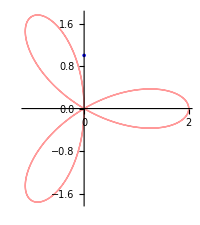

```mathematica
e13=Show[ParametricPlot[{Cos[t]+Cos[2 t],Sin[t]-Sin[2 t]},{t,-2 π,2 π},PlotStyle->{Red,Thickness[0.005],Opacity[.4]},ImageSize->200],ListPlot[{{6,1},{0,1}},PlotStyle->Blue](*,ParametricPlot[{6-8 w,1,8+6 w},{w,-1,1},PlotStyle->{Green,Thickness[0.005]}],Graphics3D[{Text["{6,1,8}",{6.7,1,8.7}]}]*)]
```

```mathematica
e1=positionfunction=r[t_]={Cos[t]+Cos[2 t],Sin[t]-Sin[2 t]}
```

{Cos[t]+Cos[2 t],Sin[t]-Sin[2 t]}

```mathematica
e2=velocityfunction=r'[t]
```

{-Sin[t]-2 Sin[2 t],Cos[t]-2 Cos[2 t]}

```mathematica
e3=accelerationfunction=r''[t]
```

{-Cos[t]-4 Cos[2 t],-Sin[t]+4 Sin[2 t]}

Above: general acceleration.

```mathematica
e4=magnitudeofvelocity=Norm[r'[t]]
```

√(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[-Sin[t]-2 Sin[2 t]]^2)

Above: magnitude of the velocity.

```mathematica
e41=velocitymagnitudesquared=e4^2
```

Abs[Cos[t]-2 Cos[2 t]]^2+Abs[-Sin[t]-2 Sin[2 t]]^2

```mathematica
e42=FullSimplify[(Cos[t]-2 Cos[2 t])^2+(-Sin[t]-2 Sin[2 t])^2==5-4 Cos[3 t]]
```

True

```mathematica
e43=5-4 Cos[3 t]
```

5-4 Cos[3 t]

Above: Mathematica verifies that the text answer for (|v|)^2 agrees with the tangled forest above. (I did remove the absolute value restrictions for the test, since they did not show up in the text answer.)

```mathematica
e5=aT=(e2.e3)/e43
```

((-Cos[t]-4 Cos[2 t]) (-Sin[t]-2 Sin[2 t])+(Cos[t]-2 Cos[2 t]) (-Sin[t]+4 Sin[2 t]))/(5-4 Cos[3 t])

```mathematica
e6=FullSimplify[e5]
```

(6 Sin[3 t])/(5-4 Cos[3 t])

Above: this would be the tangential acceleration, except it needs a v.

prime dot doubleprime divided by magnitude of velocity.

```mathematica
e8=tangentialacceleration=e6 e2
```

{(6 (-Sin[t]-2 Sin[2 t]) Sin[3 t])/(5-4 Cos[3 t]),(6 (Cos[t]-2 Cos[2 t]) Sin[3 t])/(5-4 Cos[3 t])}

Above: the actual tangential acceleration, but more complicated than the text answer.

```mathematica
e9=aN=Norm[Cross[e2,e3]]/Norm[e2]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

Norm[{-Sin[t]-2 Sin[2 t],Cos[t]-2 Cos[2 t]}×{-Cos[t]-4 Cos[2 t],-Sin[t]+4 Sin[2 t]}]/(√(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[-Sin[t]-2 Sin[2 t]]^2))

Above, oops, this is only 2 dimensional. How to get normal acceleration? Looks like I need ⅆu/ⅆs(ⅆs/dt)^2 where u is the unit tangent vector and s is the speed, or norm of velocity. And u=r'[t]/(|r'[t]|).

```mathematica
e10=u=e2/e4
```

{(-Sin[t]-2 Sin[2 t])/(√(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[-Sin[t]-2 Sin[2 t]]^2)),(Cos[t]-2 Cos[2 t])/(√(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[-Sin[t]-2 Sin[2 t]]^2))}

Above: hold on, looks like it’s getting complicated. The text mentions an easier way: normal acceleration is general acceleration minus tangential acceleration.

```mathematica
e11=e3-e6
```

{-Cos[t]-4 Cos[2 t]-(6 Sin[3 t])/(√(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[Sin[t]+4 Cos[t] Sin[t]]^2)),-Sin[t]+4 Sin[2 t]-(6 Sin[3 t])/(√(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[Sin[t]+4 Cos[t] Sin[t]]^2))}

Above: this would be the normal acceleration. How to simplify? I notice that the text does not bother to report the normal acceleration, so I could just skip it.

```mathematica
e12=FullSimplify[(Cos[t]-2 Cos[2 t])^2+(Sin[t]+4 Cos[t] Sin[t])^2]
```

5-4 Cos[3 t]

```mathematica
e13=normalacceleration=e11/.(Abs[Cos[t]-2 Cos[2 t]]^2+Abs[Sin[t]+4 Cos[t] Sin[t]]^2)->5-4 Cos[3 t]
```

{-Cos[t]-4 Cos[2 t]-(6 Sin[3 t])/(√(5-4 Cos[3 t])),-Sin[t]+4 Sin[2 t]-(6 Sin[3 t])/(√(5-4 Cos[3 t]))}

Above: that looks quite a bit better. However, I don’t see a path to anything simpler.

41.  r[t] = {Cos[t], Sin[2t], Cos[2t]}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=positionfunction=r[t_]={Cos[t],Sin[2 t],Cos[2 t]}
```

{Cos[t],Sin[2 t],Cos[2 t]}

```mathematica
e2=velocityfunction=r'[t]
```

{-Sin[t],2 Cos[2 t],-2 Sin[2 t]}

```mathematica
e3=accelerationfunction=r''[t]
```

{-Cos[t],-4 Sin[2 t],-4 Cos[2 t]}

Above: general acceleration.

```mathematica
e4=magnitudeofvelocity=Norm[r'[t]]
```

√(4 Abs[Cos[2 t]]^2+Abs[Sin[t]]^2+4 Abs[Sin[2 t]]^2)

Above: magnitude of the velocity.

```mathematica
e5=squareofvelocity=e4^2
```

4 Abs[Cos[2 t]]^2+Abs[Sin[t]]^2+4 Abs[Sin[2 t]]^2

```mathematica
e6=e5/.(4 Abs[Cos[2 t]]^2+Abs[Sin[t]]^2+4 Abs[Sin[2 t]]^2)->4+Sin[t]^2
```

4+Sin[t]^2

Above: hand simplification.

```mathematica
e6=(e2.e3)/e6
```

(Cos[t] Sin[t])/(4+Sin[t]^2)

Above: tangential acceleration, but it is incomplete, because it needs to be multiplied by v.

```mathematica
e7=e6 e2
```

{-(Cos[t] Sin[t]^2)/(4+Sin[t]^2),(2 Cos[t] Cos[2 t] Sin[t])/(4+Sin[t]^2),-(2 Cos[t] Sin[t] Sin[2 t])/(4+Sin[t]^2)}

```mathematica
e7=normalacceleration=Norm[Cross[e2,e3]]/Norm[e2]
```

(√(Abs[-4 Cos[2 t] Sin[t]+2 Cos[t] Sin[2 t]]^2+Abs[2 Cos[t] Cos[2 t]+4 Sin[t] Sin[2 t]]^2+Abs[-8 Cos[2 t]^2-8 Sin[2 t]^2]^2))/(√(4 Abs[Cos[2 t]]^2+Abs[Sin[t]]^2+4 Abs[Sin[2 t]]^2))

Again, normal acceleration is a mess. Try it the other way.

```mathematica
e8=normalacceleration=e3-e6
```

{-Cos[t]-(Cos[t] Sin[t])/(4+Sin[t]^2),-(Cos[t] Sin[t])/(4+Sin[t]^2)-4 Sin[2 t],-4 Cos[2 t]-(Cos[t] Sin[t])/(4+Sin[t]^2)}

```mathematica
e9=FullSimplify[e8]
```

{Cos[t] (-1+(2 Sin[t])/(-9+Cos[2 t])),(-4+1/(-9+Cos[2 t])) Sin[2 t],-4 Cos[2 t]+Sin[2 t]/(-9+Cos[2 t])}

Above: I don’t see much to choose between e8 and e9.

```mathematica
e10=ParametricPlot3D[{Cos[t],Sin[2 t],Cos[2 t]},{t,0,2 π},PlotStyle->{Red,Thickness[0.005],Opacity[.4]},ImageSize->300]
```

-Graphics3D-

43.  Sun and Earth. Find the acceleration of the Earth toward the sun from numbered line (19) on p. 387 and the fact that Earth revolves about the sun in a nearly circular orbit with an almost constant speed of 30 km/s.

45.  Satellite. Find the speed of an artificial Earth satellite traveling at an altitude of 80 miles above Earth’s surface, where g = 31 ft/sec^2. (The radius of the Earth is 3960 miles.)

47 - 55 Curvature and torsion

47.  Circle. Show that a circle of radius a has a curvature 1/a.

49.  Plane curve. Using numbered line (22) on p. 389, show that for a curve y = f[x]

κ[x]=(|y''|)/((1+(y')^2)^(3/2)) where (y'=dy/dx, etc.)

Note: Problem 49 calls for reference to numbered line (22*), but no such numbered line exists in the present section. Numbered line (22) looks like it deals with related matter and it reads: κ(s)=|u'(s)|=|r''(s)|